```mathematica
Needs["PlotLegends`"]
```

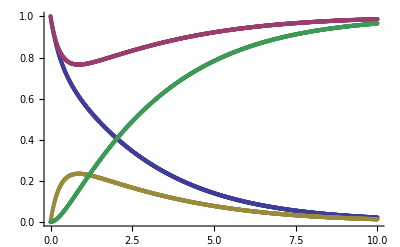

```mathematica
data = ReadList["/home/jhofman/Desktop/Project/basiceq.txt",{Number,Number,Number,Number,Number}];
S = Drop[data,None,-3];
En = Drop[Drop[data,None,{2}],None,-2];
ES = Drop[Drop[data,None,{2,3}],None,-1];
P = Drop[data,None,{2,4}];

ListPlot[{S,En,ES,P},PlotLegend->{"S","E","ES","P"},LegendPosition->{1.1,-0.4}]
```

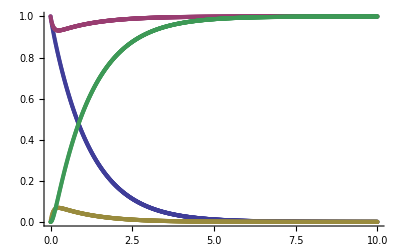

```mathematica
data = ReadList["/home/jhofman/Desktop/Project/basicrp.txt",{Number,Number,Number,Number,Number}];
S = Drop[data,None,-3];
En = Drop[Drop[data,None,{2}],None,-2];
ES = Drop[Drop[data,None,{2,3}],None,-1];
P = Drop[data,None,{2,4}];

ListPlot[{S,En,ES,P},PlotLegend->{"S","E","ES","P"},LegendPosition->{1.1,-0.4}]
```

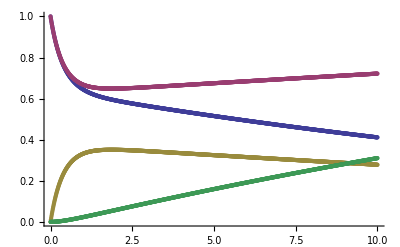

```mathematica
data = ReadList["/home/jhofman/Desktop/Project/basicrm.txt",{Number,Number,Number,Number,Number}];
S = Drop[data,None,-3];
En = Drop[Drop[data,None,{2}],None,-2];
ES = Drop[Drop[data,None,{2,3}],None,-1];
P = Drop[data,None,{2,4}];

ListPlot[{S,En,ES,P},PlotLegend->{"S","E","ES","P"},LegendPosition->{1.1,-0.4}]
```

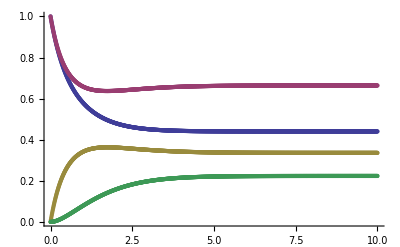

```mathematica
data = ReadList["/home/jhofman/Desktop/Project/basicfb.txt",{Number,Number,Number,Number,Number}];
S = Drop[data,None,-3];
En = Drop[Drop[data,None,{2}],None,-2];
ES = Drop[Drop[data,None,{2,3}],None,-1];
P = Drop[data,None,{2,4}];

ListPlot[{S,En,ES,P},PlotLegend->{"S","E","ES","P"},LegendPosition->{1.1,-0.4},PlotRange->All]
```

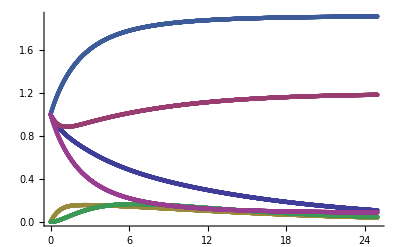

```mathematica
data = ReadList["/home/jhofman/Desktop/Project/basicfbinh.txt",{Number,Number,Number,Number,Number,Number,Number}];
S = Drop[data,None,-5];
En = Drop[Drop[data,None,{2}],None,-4];
ES = Drop[Drop[data,None,{2,3}],None,-3];
P = Drop[Drop[data,None,{2,4}],None,-2];
Inh = Drop[Drop[data,None,{2,5}],None,-1];
EInh = Drop[data,None,{2,6}];

ListPlot[{S,En,ES,P,Inh,EInh},PlotLegend->{"S","E","ES","P","Inh","EInh"},LegendPosition->{1.1,-0.4},PlotRange->All]
```